# 2D Tumbling Bottle

## Semi-Elastic Particle and Plane

## Newtonian Solver

Solve a bouncing particle with friction; mass m, coefficient of restitution c_r=cr, dynamic friction coefficient μ_d=mud, static friction coefficient μ_s=mus.

```mathematica
ClearAll[g];g=-9.81;
ClearAll[ms];ms=0.001(* millisecond *)
```

0.001

World frame: x to the right, z up (looking forward to 3D). Floor has the equation of a line.

Disallow penetration. 

On collision, Snell’s law sets the normal component of velocity v_n' of the ball after bounce to -c_r v_n, where v_n is the normal component of the velocity before bounce. The tangential component of velocity (momentum per unit mass) .7floses μ_d but does not change sign.

The floor gains the ball’s lost momentum.7f, but the floor is an infinite sink; momentum is conserved. 

The change in momentum’s normal component is (new momentum - old momentum) = m*(-c_r v_n - v_n) = -m v_n(1+c_r) --- Snell’s Law. This is the impulse or force*dt. Because .7f(acceleration * dt = dv) and because mass is constant in this problem, we can pun and call dv “impulse” instead of the more precise “specific impulse.” Later, with a rod whose end masses may not be the same, we avoid the pun.

TODO: add Aero drag

### Support

```mathematica
ClearAll[tangentPlane,tangentPlaneInstance,ballInstance];
On[Assert];
```

#### Tangent Speed After Dynamic Friction

Consider an initial tangential speed v_t, opposed by a frictional force -m μ_D cos(θ)v_t(t), where θ is the angle of inclination of the floor, for a finite, positive but small time dt_slide. The quantity μ_D cos(θ)v_t(t) has units of acceleration. Let c=cos(θ) and ⅆt be an infinitesimal time. The specific impulse is ⅆv_t(t)=-μ_Dc v_t(t) ⅆt, which is just Newton’s Second Law divided by the constant, positive mass m. This has solution v_t(t)=v_t(0)Exp[-μ_Dc t]. The total impulse suffered over time dt_slide is

v_t(dt_slide)-v_t(0)=v_t(0)( Exp[-μ_Dc dt_slide]-1)

Notice that ( Exp[-μ_Dc dt_slide]-1) is negative when dt_slide is positive, so the impulse opposes v_t(0) and reduces its magnitude.

The velocity after sliding is

v_t(dt_slide)=v_t(0)( Exp[-μ_Dc dt_slide]-1)+v_t(0)=v_t(0)Exp[-μ_Dc dt_slide]

which is >0 and the same sign as v_t(0).

```mathematica
ClearAll[vtPostDynamicFriction];
vtPostDynamicFriction[vt0_,μd_,c_,dtSlide_]:=
Module[{},
Assert[dtSlide≥0];
vt0 Exp[-μd c dtSlide]];
```

#### Normal Component of Speed After Semi-elastic Bounce

Snell’s Law: bounce with restitution:

v_n(t^+)=-c_rv_n(t^-)

```mathematica
ClearAll[vnPostSnellsBounce];
vnPostSnellsBounce[vn_,cr_]:=
With[{vnPre0=-cr vn},
(* Clamp result *)
With[{vnPost=If[vnPre0<0.0,
(Print[<|"ERROR"->"bounced but not rising; clamping to zero",",vnPre0"->vnPre0|>];0.0),
vnPre0]},
If[Abs[vnPost]>Abs[vn],(Print[<|
"ERROR"->"gained momentum on bounce",
"trial"->vnPost,"vn2"->vn|>])];
vnPost]];
```

#### Clamp Height

TODO: This fires a lot on the rod.

```mathematica
ClearAll[clampHeight];
clampHeight[z_,zMin_]:=
If[z<zMin,(* TODO: better with exact determinants *)
(Print[<|"ERROR"->"below floor; clamping to floor","δ"->zMin-z|>];
zMin),z];
```

#### Euler-Step State

```mathematica
ClearAll[eulerStepState];
eulerStepState[px_,pz_,vx_,vz_,dt_]:=
{px+vx dt,
pz+vz dt,
vx,
vz+g dt};
```

#### Damp Micro Bouncing

Heuristic: if it’s coming in low and slow just eat all the momentum and energy lest it bounce forever (to see micro-bouncing, set this to return {z2,vz2} always).

If it’s lower than it would free fall and its kinetic energy before and after perfectly elastic bouncing is less than it would acquire from free fall just let it rest.

```mathematica
ClearAll[dampMicroBouncing];
dampMicroBouncing[z_,zMin_,z2_,vz2_,dt_]:=
With[{dz=z-zMin},
If[(dz<-0.5g dt^2)&&(Abs[vz2]<1.4142135623730951Abs[g dt]),
{zMin,0},{z2,vz2}]];
```

#### To and From Tangent-Normal Frame

```mathematica
ClearAll[toFrame,fromFrame];
toFrame[x_,z_,s_,c_]:={(c x)+(s z),-(s x)+(c z)};
fromFrame[x_,z_,s_,c_]:={(c x)-(s z),(s x)+(c z)};
```

#### Clamp Penetration Falling Speed

```mathematica
ClearAll[clampPenFallSpeed];
clampPenFallSpeed[vz_]:=
If[vz>0.,
(Print[<|"ERROR"->"penetrating but not falling; clamping to zero","vz"->vz|>];0.0),
vz];
```

#### Clamp Penetration Falling Speed --- Tangent-Normal Frame

```mathematica
ClearAll[clampPenNormalSpeed];
clampPenNormalSpeed[vn_]:=
If[vn>0.0,
(Print[<|"ERROR"->"penetrating but not falling (tangent-normal frame); clamping to zero","vn"->vn|>];0.0),
vn];
```

#### Predict Time Until Floor Strike

Let the particle fall with initial speed mvz and acceleration maz.

```mathematica
b$=Solve[dz==mvz t+maz t^2/2,t]
```

{{t→(-mvz+√(2 dz maz+mvz^2))/maz},{t→-(mvz+√(2 dz maz+mvz^2))/maz}}

There are two solutions for the time till strike, one negative, the other positive. The negative solution tells us, if the ball had penetrated, how long ago. We don’t allow penetration, so we only want the positive solution.

```mathematica
Manipulate[b$/.{mvz->mvz2,dz->dz2,maz->-g},{{mvz2,14.},0.0,20.0,Appearance->"Labeled"},{{dz2,0.03},0.0,1.0,Appearance->"Labeled"}]
```

The positive solution is (-mvz+Sqrt[...])/(-g)=(v_z+Sqrt[...])/(-g) when v_z is non-positive, as it must always be.

```mathematica
ClearAll[floorStrike];
floorStrike[z_,zMin_,vz_,dt_]:=
With[{dz=z-zMin},
Assert[dz≥0.0];
Assert[vz≤0.0];
Assert[g<0.0];
With[{Δ=2(-g) dz+vz^2},
If[Δ<0.0,
(Print[<|"ERROR"->"Negative discriminant; clamping to zero",
"Δ"->Δ,"Abs[vz dt]"->Abs[vz dt],"2 g dz"->2g dz,"vz^2"->vz^2,"dz"->dz|>];
0.0),
With[{dts=(vz+Sqrt[Δ])/-g},
Assert[dts≥0.0];
If[dts>dt,
(Print[<|"ERROR"->"dtStrike too large; clamping to zero",
"Δ"->Δ,"Abs[vz dt]"->Abs[vz dt],"2 g dz"->2g dz,"vz^2"->vz^2,
"dzFloor"->dz,"vz"->vz,"dtStrike"->dts,"otherSoln"->(-vz+Sqrt[Δ])/-g,"dt"->dt|>];
0.0),
dts]]]]];
```

#### Clamp Normal Component of Position

```mathematica
ClearAll[clampNormalPos];
clampNormalPos[z_,zMin_]:=
If[z<zMin,(Print[<|"ERROR"->"bounced but still low; clamping to floor","pn2p"->z,"pzFloor"->zMin|>];
zMin),
z];
```

#### Tangential Position

```mathematica
ClearAll[tangentPos];
tangentPos[px_,pz_,vx_,vz_,s_,c_,dtStrike_,dt_,vt2post_]:=
With[{pt=(c px)+(s pz),vt=(c vx)+(s vz)},
pt+vt dtStrike+vt2post(dt-dtStrike)];
```

#### Tangent Plane Constants

```mathematica
ClearAll[tangentPlane];
tangentPlane[slope_,intercept_]:=
With[{r=√(1+slope^2)},
tangentPlaneInstance[slope,intercept,slope/r,1/r]];
```

#### Bounce State

If the ball is going to bounce, do an analytical solution for the post-bounce state (or high-precision numerical, if we include aero drag TODO).

```mathematica
ClearAll[bounceState];
bounceState[px_,pz_,pzFloor_,vx_,vx2_,vzI_,vz2_,cr_,mud_,dt_,s_,c_]:=
Module[{pt,pt2p,    pn2p0,pn2p,    vt2,vt2p,   vz,    vn20,vn2,    vn2p0,vn2p,    dtStrike},
Assert[pz≥pzFloor];
vz=clampPenFallSpeed[vzI];
{vt2,vn20}=toFrame[vx2,vz2,s,c];
vn2=clampPenNormalSpeed[vn20];
dtStrike=floorStrike[pz,pzFloor,vz,dt];
(* Heuristic --- it slides for dt-dtStrike --- is this right? *)
vt2p=vtPostDynamicFriction[vt2,mud,c,dt-dtStrike];
vn2p=vnPostSnellsBounce[vn2,cr];
With[{ddt=dt-dtStrike},
pn2p0=pzFloor+vn2p*ddt+g ddt^2/2.0];
pn2p=clampNormalPos[pn2p0,pzFloor];
pt2p=tangentPos[px,pz,vx,vz,s,c,dtStrike,dt,vt2p];
Join[fromFrame[pt2p,pn2p,s,c],fromFrame[vt2p,vn2p,s,c]]];
```

### Euler-Step Ball With All Effects

```mathematica
ClearAll[eulerStepBall];
eulerStepBall[state:{px_,pz_,vx_,vzI_},dt_,
ball:ballInstance[m_,cr_,mud_,mus_],
floor:tangentPlaneInstance[slope_,intercept_,s_,c_]]:=
Module[{pzFloor,
px2,    p,pz20,pz2,    vx2,    vz20,vz2},
{px2,pz20,vx2,vz20}=eulerStepState[px,pz,vx,vzI,dt];
pzFloor=slope*px2+intercept;
{pz2,vz2}=dampMicroBouncing[pz,pzFloor,pz20,vz20,dt];
If[pz2<pzFloor,
bounceState[px,pz,pzFloor,vx,vx2,vzI,vz2,cr,mud,dt,s,c],
{px2,pz2,vx2,vz2}]];
```

## Demonstrations

### Initial Conditions

```mathematica
ClearAll[state0,ball0,floor0];
state0={1.,10,1.0,0};ball0=ballInstance[1.,0.80,0.20,1.0];floor0=tangentPlane[0.0,0.0];
```

### Support

#### Euler Stepper Maker (Foldable Closure)

This is a “foldable:” a binary function of state and dt that closes over constants.

```mathematica
ClearAll[eulerBallStepperMaker];
eulerBallStepperMaker[ball_,floor_]:=
Function[{state,dt},eulerStepBall[state,dt,ball,floor]];
```

#### Projectors

```mathematica
ClearAll[pickPos,pickVel,column,huePoints];
pickPos[state:{x_,z_,_,_}]:={x,z};
pickVel[state:{_,_,vx_,vz_}]:={vx,vz};
column[n_]:=Function[arrs,#[[n]]&/@arrs];
huePoints[n_]:=MapIndexed[Style[#1,Hue[(2./3.)#2/n]]&];
```

### Simulate a Single Ball

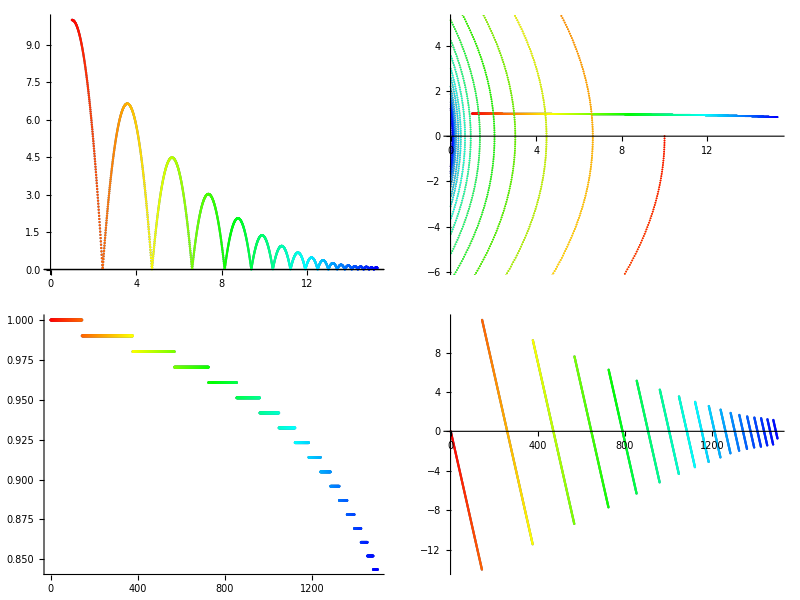

```mathematica
ClearAll[simSingleBall];
simSingleBall[state0s_,dt_,n_,
ball:ballInstance[m_,cr_,mud_,mus_],
floor:tangentPlaneInstance[slope_,intercept_,_,_],slowTimeHue_:False]:=
With[{soln=FoldList[eulerBallStepperMaker[ball,floor],state0s,ConstantArray[dt,n]]},
With[{poss=pickPos/@soln,vels=pickVel/@soln},
With[{xphases=Transpose[{column[1]@poss,column[1]@vels}],
zphases=Transpose[{column[2]@poss,column[2]@vels}]},
Grid[{{ListPlot[If[slowTimeHue,huePoints[n]@poss,poss],
PlotRange->{Automatic,Automatic},
Epilog->{Line[{{-100,slope*(-100)+intercept},{100,slope*(100)+intercept}}]},ImageSize->Medium],
ListPlot[{If[slowTimeHue,huePoints[n][xphases],xphases],
If[slowTimeHue,huePoints[n][zphases],zphases]},ImageSize->Medium]
},{ListPlot[If[slowTimeHue,huePoints[n][column[1][vels]],column[1][vels]],
PlotRange->{Automatic,Automatic},ImageSize->Medium],ListPlot[{If[slowTimeHue,huePoints[n][column[2][vels]],column[2][vels]]},
PlotRange->{Automatic,Automatic},ImageSize->Medium]
}}]    ]]];
simSingleBall[state0,10ms,1500,ballInstance[1.,0.80,1.0,1.0],floor0,True]
```

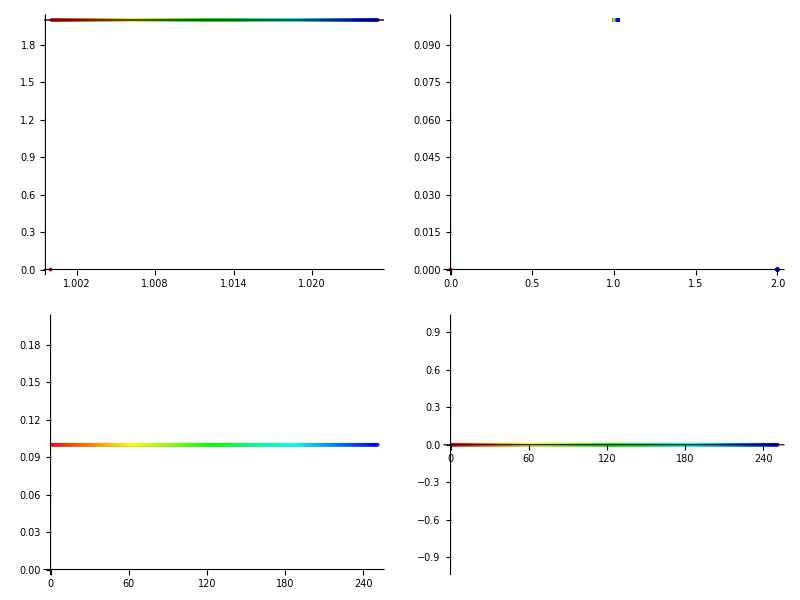

```mathematica
simSingleBall[{1.,.0,.1,0},1ms,250,
ballInstance[1.,.80,0.20,1.0],
tangentPlane[0.,2.0],True]
```

With slope down to the right:

```mathematica
simSingleBall[state0,10ms,1000,ball0,
tangentPlane[-0.05,2.0],True]
```

<|ERROR→bounced but still low; clamping to floor,pn2p→1.56495,pzFloor→1.56501|>

<|ERROR→Negative discriminant; clamping to zero,Δ→-8.46286,Abs[vz dt]→0.000872831,2 g dz→8.47048,vz^2→0.00761833,dz→-0.431727|>

<|ERROR→bounced but still low; clamping to floor,pn2p→1.56365,pzFloor→1.5637|>

<|ERROR→Negative discriminant; clamping to zero,Δ→-8.48849,Abs[vz dt]→0.000872663,2 g dz→8.49611,vz^2→0.0076154,dz→-0.433033|>

<|ERROR→bounced but still low; clamping to floor,pn2p→1.56235,pzFloor→1.5624|>

<|ERROR→Negative discriminant; clamping to zero,Δ→-8.51412,Abs[vz dt]→0.000872495,2 g dz→8.52173,vz^2→0.00761247,dz→-0.434339|>

<|ERROR→bounced but still low; clamping to floor,pn2p→1.56104,pzFloor→1.5611|>

$Aborted

With small slope down to the left:

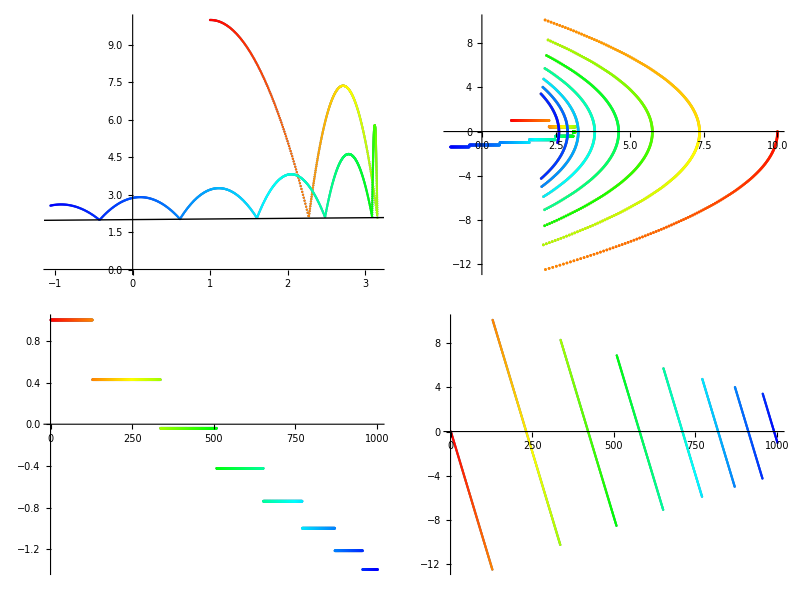

```mathematica
simSingleBall[state0,10ms,1000,
ballInstance[1.,0.80,1.0,1.0],
tangentPlane[0.025,2.0],True]
```

Small slope, no dynamic friction:

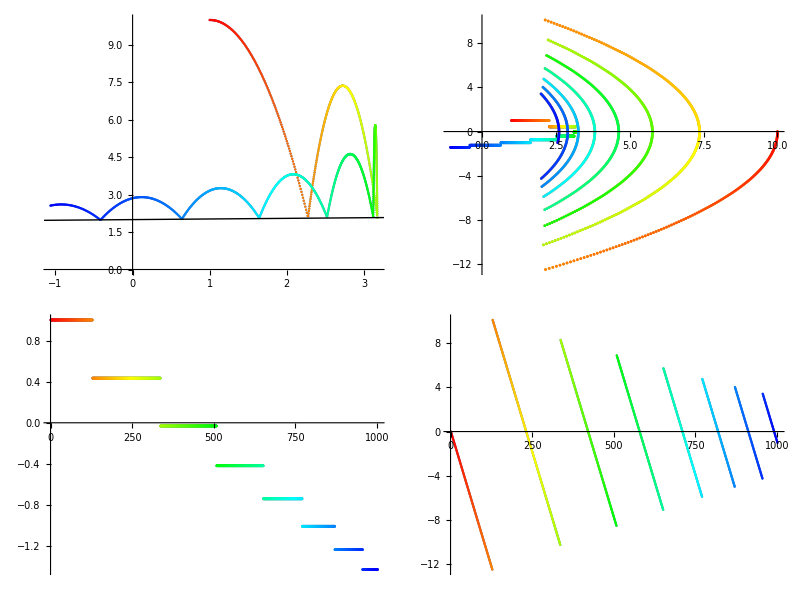

```mathematica
simSingleBall[{1.,10,1.0,0},10ms,1000,
ballInstance[1.,0.80,0,1.0],(* no dynamic friction *)
tangentPlane[0.025,2.0],True]
```

### Animate a Single Ball

```mathematica
ClearAll[animSimBall];
(*animSimBall[state_,ball_,floor:tangentPlaneInstance[_,_,_,_]]:=
DynamicModule[{ψ=state,stepper=eulerBallStepperMaker[ball,floor],graphics},
Dynamic[ψ=stepper[ψ,10ms]]];
animSimBall[{1.,.0,1.0,0},ball0,floor0]*)
```

```mathematica
ClearAll[animSimBall];
animSimBall[state_,ball_,floor:tangentPlaneInstance[slope_,intercept_,_,_]]:=
DynamicModule[{ψ=state,stepper=eulerBallStepperMaker[ball,floor],graphics},
Dynamic[
With[{x=ψ⟦1;;2⟧},
graphics=GraphicsRow[{
Show[Graphics[{
Black,Line[{{-100,slope*(-100)+intercept},{100,slope*(100)+intercept}}],
Blue,Disk[x,0.1]}],
PlotRange->{{-1,11},{-1,11}},ImageSize->Medium],
Show[Graphics[{Black,Line[{{-2,0},{2,0}}],
Blue,Disk[{ψ⟦1⟧,ψ⟦3⟧},0.1],
Red,Disk[{ψ⟦2⟧,ψ⟦4⟧},0.1]}],
PlotRange->{{-2,2},{-2,2}}]    }]    ];
ψ=stepper[ψ,10ms];graphics]];
animSimBall[{1.,.0,1.0,0},ball0,floor0]
```

## Rigid, Massless Rod

TODO: The approach here tried to reuse the ball. Not working out well. going to a more principled solution for the truss. Let the rod be a special case.

## Newtonian Solver

TODO: Lagrangian solver.

### Center-of-Mass Frame

```mathematica
With[{xLim=10,mLim=10,zSpan=2.5,hiText=2,loText=-3,lineText=-0.5},
DynamicModule[{xcm,cm},
Manipulate[
xcm=xLim mr/(ml+mr);cm={xcm,0};
Show[{Graphics[{Opacity[0.25],Disk[{0,0},ml],Disk[{xLim,0},mr],
Opacity[1.0],Red,Disk[cm,0.75],Black,Line[{{0,0},{xLim,0}}],
Line[{{0,-zSpan},{0,zSpan}}],Line[{{xcm,-zSpan},{xcm,zSpan}}],Line[{{xLim,-zSpan},{xLim,zSpan}}],
Blue,Text[cm/xLim,{xcm,hiText}],
Text["xLrod",{xcm/2,lineText}],Text["xRrod",{(xLim+xcm)/2,lineText}]
}]
},PlotRange->{{-2,1.2xLim},{-4,4}}],
{{ml,1},0,mLim,1},{{mr,2},0,mLim,1}]]]
```

### Data Types

Use vectors internally. At interface, use state-space form (dynamical variables flattened into.7f.7f.7f a single vector).

```mathematica
ClearAll[rigidMasslessRodInstance,rigidMasslessRod,eulerStepRigidMasslessRod,eulerRigidMasslessRodStepperMaker,simSingleRigidMasslessRod];
```

#### Constructor for Rigid, Massless Rod

```mathematica
rigidMasslessRod[
rigidMasslessRodInstance[
ballInstance[mL_,crL_,mudL_,musL_],
ballInstance[mR_,crR_,mudR_,musR_],
rodLength_]]:=
With[{mTotal=mL+mR},
With[{xLrod=-rodLength mR/mTotal},
With[{xRrod=rodLength+xLrod},
With[{mi=mL xLrod^2+mR xRrod^2},
rigidMasslessRodInstance[
ballInstance[mL,crL,mudL,musL],
ballInstance[mR,crR,mudR,musR],
rodConstants[mTotal,xLrod,xRrod,mi,rodLength]]]]]];
```

### Support Routines

#### Two-Dimensional Cross Product

```mathematica
ClearAll[cross2D];
cross2D[{a_,b_},{c_,d_}]:=a d-b c;
```

#### Impulse at a Rod End

```mathematica
ClearAll[specificImpulseRodEnd,impulseRodEnd];
```

```mathematica
specificImpulseRodEnd[px_,pzI_,vx_,vzI_,
ballInstance[m_,cr_,mud_,mus_],
tangentPlaneInstance[slope_,intercept_,s_,c_],dt_]:=
Module[{pzFloor=slope*px+intercept,
px2,    pz,pz20,pz2,    vx2,    vz20,vz2},
pz=clampHeight[pzI,pzFloor];
{px2,pz20,vx2,vz20}=eulerStepState[px,pz,vx,vzI,dt];
{pz2,vz2}=dampMicroBouncing[pz,pzFloor,pz20,vz20,dt];
If[pz2<pzFloor,
Module[{pt2p,pn2p,vt2p,vn2p,vt,vn,px2p,pz2p},
{pt2p,pn2p,vt2p,vn2p}=bounceState[px,pz,pzFloor,vx,vx2,vzI,vz2,cr,mud,dt,s,c];
{vt,vn}=toFrame[vx,vzI,s,c];
{px2p,pz2p}=fromFrame[pt2p,pn2p,s,c];
Assert[pz2p≥pzFloor];
Join[{px2p,pz2p},
fromFrame[vt2p-vt,vn2p-vn,s,c],
{True}]],
{px2,pz2,0.0,g dt,False}]];
impulseRodEnd[px_,pzI_,vx_,vz_,
ballInstance[m_,cr_,mud_,mus_],
tangentPlaneInstance[slope_,intercept_,s_,c_],dt_]:=
Module[{px2,pz2,ix2,iz2,bounceQ},
{px2,pz2,ix2,iz2,bounceQ}= specificImpulseRodEnd[px,pzI,vx,vz,
ballInstance[m,cr,mud,mus],
tangentPlaneInstance[slope,intercept,s,c],dt];
{px2,pz2,m ix2,m iz2,bounceQ}];
```

### Euler Step Rigid Massless Rod Solver

Inputs are flattened for state-space form.

```mathematica
ClearAll[eulerStepRigidMasslessRod];
eulerStepRigidMasslessRod[
{xcm_,zcm_,vxcm_,vzcm_,θ_,ω_},dt_,
rigidMasslessRodInstance[
ballInstance[mL_,crL_,mudL_,musL_],
ballInstance[mR_,crR_,mudR_,musR_],
rodConstants[mTotal_,xLrod_,xRrod_,mi_,rodLength_]],
tangentPlaneInstance[slope_,intercept_,s_,c_]]:=
With[{cθ=Cos[θ],sθ=Sin[θ],cm={xcm,zcm},vcm={vxcm,vzcm}},
With[{xLcm=xLrod{cθ,sθ},xRcm=xRrod{cθ,sθ}},
Module[{xL,zL,vxL,vzL,xR,zR,vxR,vzR,
x2L,z2L,vx2L,vz2L,ixL,izL,bounceQL,
x2R,z2R,vx2R,vz2R,ixR,izR,bounceQR},
{xL,zL}=cm+xLcm;
{xR,zR}=cm+xRcm;
{vxL,vzL}=vcm+ω xLrod{sθ,-cθ};(* xy cross product, y into page *)
{vxR,vzR}=vcm+ω xRrod{sθ,-cθ};(* xy cross product, y into page *)
{x2L,z2L,ixL,izL,bounceQL}=impulseRodEnd[xL,zL,vxL,vzL,
ballInstance[mL,crL,mudL,musL],
tangentPlaneInstance[slope,intercept,s,c],dt];
{x2R,z2R,ixR,izR,bounceQR}=impulseRodEnd[xR,zR,vxR,vzR,
ballInstance[mR,crR,mudR,musR],
tangentPlaneInstance[slope,intercept,s,c],dt];
Module[{τiL,τiR,θ2,ω2,xcm2,zcm2,vxcm2,vzcm2},
τiL=cross2D[{ixL,izL},xLcm];
τiR=cross2D[{ixR,izR},xRcm];
xcm2=(x2L mL+x2R mR)/mTotal;
zcm2=(z2L mL+z2R mR)/mTotal;
vxcm2=vxcm+(ixL+ixR)/mTotal;
vzcm2=vzcm+(izL+izR)/mTotal;
θ2=ArcTan[x2R-x2L,z2R-z2L];(* TODO: avoid ArcTan? *)
ω2=ω+(τiL+τiR)/mi;
{xcm2,zcm2,vxcm2,vzcm2,θ2,ω2}]]]];
```

## Demonstrations

### Initial Conditions

```mathematica
ClearAll[rod0];
rod0=rigidMasslessRod[
rigidMasslessRodInstance[
ballInstance[1.0,0.75,0.15,1.0],
ballInstance[2.0,0.85,0.25,1.0],2.0]];
```

```mathematica
ClearAll[rodState0];
rodState0={0.0,10.0,1.0,0.0,10°,0.0}
```

{0.,10.,1.,0.,10 °,0.}

### Support Routines

#### Euler Stepper Maker (Foldable Closure)

```mathematica
ClearAll[eulerRigidMasslessRodStepperMaker];
eulerRigidMasslessRodStepperMaker[rod_,floor_]:=
Function[{state,dt},eulerStepRigidMasslessRod[state,dt,rod,floor]];
```

#### Projectors

```mathematica
ClearAll[pickCmPos,pickCmVel,pickθ,pickω];
pickCmPos[{xcm_,zcm_,_,_,_,_}]:={xcm,zcm};
pickCmVel[_,_,vxcm_,vzcm_,_,_]:={vxcm,vzcm};
pickθ[{_,_,_,_,θ_,_}]:=θ;
pickω[{_,_,_,_,_,ω_}]:=ω;
```

#### Rod End Positions

```mathematica
ClearAll[endPoss];
endPoss[{xcm_,zcm_,vxcm_,vzcm_,θ_,ω_},
rigidMasslessRodInstance[
ballInstance[mL_,crL_,mudL_,musL_],
ballInstance[mR_,crR_,mudR_,musR_],
rodConstants[mTotal_,xLrod_,xRrod_,mi_,rodLength_]]]:=With[{cθ=Cos[θ],sθ=Sin[θ],cm={xcm,zcm}},
With[{xLcm=xLrod{cθ,sθ},xRcm=xRrod{cθ,sθ}},
{cm+xLcm,cm+xRcm}]];
```

### Sanity Calls

```mathematica
sanityRod$=eulerRigidMasslessRodStepperMaker[rod0,floor0][rodState0,10ms]
```

{0.01,10.,1.,-0.0981,0.174533,1.04083×10^-17}

```mathematica
endPoss[sanityRod$,rod0]
```

{{-1.30308,9.76847},{0.666539,10.1158}}

### Simulate Single Rigid Massless Rod

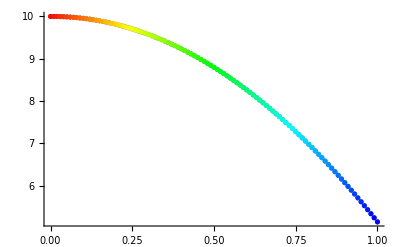

```mathematica
ClearAll[simSingleRigidMasslessRod];
simSingleRigidMasslessRod[
state:{xcm_,zcm_,vxcm_,vzcm_,θ_,ω_},dt_,n_,
rod:rigidMasslessRodInstance[
ballInstance[mL_,crL_,mudL_,musL_],
ballInstance[mR_,crR_,mudR_,musR_],
rodConstants[mTotal_,xLrod_,xRrod_,mi_,rodLength_]],
floor:tangentPlaneInstance[slope_,intercept_,s_,c_]]:=With[{    soln=FoldList[
eulerRigidMasslessRodStepperMaker[rod,floor],
state,ConstantArray[dt,n]]    },
With[{poss=pickCmPos/@soln,vels=pickCmVel/@soln,
θs=pickθ/@soln,ωs=pickω/@soln},
Grid[{{ListPlot[huePoints[n]@poss]}}]]];
simSingleRigidMasslessRod[rodState0,10ms,100,rod0,floor0]
```

### Animate Single Rigid Massless Rod

```mathematica
On[Assert];
```

```mathematica
ClearAll[animSingleRigidMasslessRod];
animSingleRigidMasslessRod[
state:{xcm_,zcm_,vxcm_,vzcm_,θ_,ω_},dt_,n_,
rod:rigidMasslessRodInstance[
ballInstance[mL_,crL_,mudL_,musL_],
ballInstance[mR_,crR_,mudR_,musR_],
rodConstants[mTotal_,xLrod_,xRrod_,mi_,rodLength_]],
floor:tangentPlaneInstance[slope_,intercept_,s_,c_]]:=With[    {soln=FoldList[
eulerRigidMasslessRodStepperMaker[rod,floor],
state,ConstantArray[dt,n]]},
Manipulate[
Show[{
Graphics[Line[{{-2,slope*(-2)+intercept},
{12,slope*12+intercept}}]],
With[{ps=endPoss[soln⟦i⟧,rod]},
Graphics[{Line[ps],
Hue[(2./3.)i/n],Disk[ps⟦1⟧,mL 0.10],Disk[ps⟦2⟧,mR 0.10]}]]},
PlotRange->{{-2,12},{-2,12}
}],{i,1,n,1,Appearance->{"Open","Labeled"}}]    ];
animSingleRigidMasslessRod[rodState0,1ms,6000,rod0,floor0]
```

<|ERROR→below floor; clamping to floor,δ→0.00271477|>

<|ERROR→below floor; clamping to floor,δ→0.00426597|>

<|ERROR→below floor; clamping to floor,δ→0.00527255|>

<|ERROR→below floor; clamping to floor,δ→0.00592299|>

<|ERROR→below floor; clamping to floor,δ→0.00634064|>

<|ERROR→below floor; clamping to floor,δ→0.00660617|>

<|ERROR→below floor; clamping to floor,δ→0.00677233|>

<|ERROR→below floor; clamping to floor,δ→0.00687356|>

<|ERROR→below floor; clamping to floor,δ→0.00693235|>

<|ERROR→below floor; clamping to floor,δ→0.00696336|>

<|ERROR→below floor; clamping to floor,δ→0.00697616|>

<|ERROR→below floor; clamping to floor,δ→0.00697696|>

<|ERROR→below floor; clamping to floor,δ→0.00696982|>

<|ERROR→below floor; clamping to floor,δ→0.00695736|>

<|ERROR→below floor; clamping to floor,δ→0.00694129|>

<|ERROR→below floor; clamping to floor,δ→0.00692273|>

<|ERROR→below floor; clamping to floor,δ→0.00690239|>

<|ERROR→below floor; clamping to floor,δ→0.00688073|>

<|ERROR→below floor; clamping to floor,δ→0.00685808|>

<|ERROR→below floor; clamping to floor,δ→0.00683461|>

<|ERROR→below floor; clamping to floor,δ→0.00681045|>

<|ERROR→below floor; clamping to floor,δ→0.0067857|>

<|ERROR→below floor; clamping to floor,δ→0.00676041|>

<|ERROR→below floor; clamping to floor,δ→0.00673461|>

<|ERROR→below floor; clamping to floor,δ→0.00670833|>

<|ERROR→below floor; clamping to floor,δ→0.00668159|>

<|ERROR→below floor; clamping to floor,δ→0.00665441|>

<|ERROR→below floor; clamping to floor,δ→0.00662678|>

<|ERROR→below floor; clamping to floor,δ→0.00659873|>

<|ERROR→below floor; clamping to floor,δ→0.00657026|>

<|ERROR→below floor; clamping to floor,δ→0.00654137|>

<|ERROR→below floor; clamping to floor,δ→0.00651207|>

<|ERROR→below floor; clamping to floor,δ→0.00648238|>

<|ERROR→below floor; clamping to floor,δ→0.00645229|>

<|ERROR→below floor; clamping to floor,δ→0.00642182|>

<|ERROR→below floor; clamping to floor,δ→0.00639097|>

<|ERROR→below floor; clamping to floor,δ→0.00635974|>

<|ERROR→below floor; clamping to floor,δ→0.00632815|>

<|ERROR→below floor; clamping to floor,δ→0.0062962|>

<|ERROR→below floor; clamping to floor,δ→0.0062639|>

<|ERROR→below floor; clamping to floor,δ→0.00623125|>

<|ERROR→below floor; clamping to floor,δ→0.00619827|>

<|ERROR→below floor; clamping to floor,δ→0.00616497|>

<|ERROR→below floor; clamping to floor,δ→0.00613134|>

<|ERROR→below floor; clamping to floor,δ→0.0060974|>

<|ERROR→below floor; clamping to floor,δ→0.00606316|>

<|ERROR→below floor; clamping to floor,δ→0.00602862|>

<|ERROR→below floor; clamping to floor,δ→0.0059938|>

<|ERROR→below floor; clamping to floor,δ→0.00595869|>

<|ERROR→below floor; clamping to floor,δ→0.00592332|>

<|ERROR→below floor; clamping to floor,δ→0.00588769|>

<|ERROR→below floor; clamping to floor,δ→0.00585181|>

<|ERROR→below floor; clamping to floor,δ→0.00581569|>

<|ERROR→below floor; clamping to floor,δ→0.00577933|>

<|ERROR→below floor; clamping to floor,δ→0.00574275|>

<|ERROR→below floor; clamping to floor,δ→0.00570596|>

<|ERROR→below floor; clamping to floor,δ→0.00566895|>

<|ERROR→below floor; clamping to floor,δ→0.00563176|>

<|ERROR→below floor; clamping to floor,δ→0.00559437|>

<|ERROR→below floor; clamping to floor,δ→0.00555681|>

<|ERROR→below floor; clamping to floor,δ→0.00551907|>

<|ERROR→below floor; clamping to floor,δ→0.00548118|>

<|ERROR→below floor; clamping to floor,δ→0.00544314|>

<|ERROR→below floor; clamping to floor,δ→0.00540496|>

<|ERROR→below floor; clamping to floor,δ→0.00536664|>

<|ERROR→below floor; clamping to floor,δ→0.00532821|>

<|ERROR→below floor; clamping to floor,δ→0.00528966|>

<|ERROR→below floor; clamping to floor,δ→0.005251|>

<|ERROR→below floor; clamping to floor,δ→0.00521225|>

<|ERROR→below floor; clamping to floor,δ→0.00517342|>

<|ERROR→below floor; clamping to floor,δ→0.0051345|>

<|ERROR→below floor; clamping to floor,δ→0.00509552|>

<|ERROR→below floor; clamping to floor,δ→0.00505648|>

<|ERROR→below floor; clamping to floor,δ→0.00501739|>

<|ERROR→below floor; clamping to floor,δ→0.00497825|>

<|ERROR→below floor; clamping to floor,δ→0.00493909|>

<|ERROR→below floor; clamping to floor,δ→0.00489989|>

<|ERROR→below floor; clamping to floor,δ→0.00486068|>

<|ERROR→below floor; clamping to floor,δ→0.00482147|>

<|ERROR→below floor; clamping to floor,δ→0.00478225|>

<|ERROR→below floor; clamping to floor,δ→0.00474303|>

<|ERROR→below floor; clamping to floor,δ→0.00470384|>

<|ERROR→below floor; clamping to floor,δ→0.00466466|>

<|ERROR→below floor; clamping to floor,δ→0.00462552|>

<|ERROR→below floor; clamping to floor,δ→0.00458642|>

<|ERROR→below floor; clamping to floor,δ→0.00454735|>

<|ERROR→below floor; clamping to floor,δ→0.00450835|>

<|ERROR→below floor; clamping to floor,δ→0.0044694|>

<|ERROR→below floor; clamping to floor,δ→0.00443052|>

<|ERROR→below floor; clamping to floor,δ→0.00439171|>

<|ERROR→below floor; clamping to floor,δ→0.00435298|>

<|ERROR→below floor; clamping to floor,δ→0.00431433|>

<|ERROR→below floor; clamping to floor,δ→0.00427578|>

<|ERROR→below floor; clamping to floor,δ→0.00423733|>

<|ERROR→below floor; clamping to floor,δ→0.00419898|>

<|ERROR→below floor; clamping to floor,δ→0.00416074|>

<|ERROR→below floor; clamping to floor,δ→0.00412261|>

<|ERROR→below floor; clamping to floor,δ→0.00408461|>

<|ERROR→below floor; clamping to floor,δ→0.00404674|>

<|ERROR→below floor; clamping to floor,δ→0.00400899|>

<|ERROR→below floor; clamping to floor,δ→0.00397138|>

<|ERROR→below floor; clamping to floor,δ→0.00393392|>

<|ERROR→below floor; clamping to floor,δ→0.0038966|>

<|ERROR→below floor; clamping to floor,δ→0.00385943|>

<|ERROR→below floor; clamping to floor,δ→0.00382241|>

<|ERROR→below floor; clamping to floor,δ→0.00378556|>

<|ERROR→below floor; clamping to floor,δ→0.00374887|>

<|ERROR→below floor; clamping to floor,δ→0.00371234|>

<|ERROR→below floor; clamping to floor,δ→0.00367599|>

<|ERROR→below floor; clamping to floor,δ→0.00363981|>

<|ERROR→below floor; clamping to floor,δ→0.00360381|>

<|ERROR→below floor; clamping to floor,δ→0.00356799|>

<|ERROR→below floor; clamping to floor,δ→0.00353236|>

<|ERROR→below floor; clamping to floor,δ→0.00349691|>

<|ERROR→below floor; clamping to floor,δ→0.00346166|>

<|ERROR→below floor; clamping to floor,δ→0.00342659|>

<|ERROR→below floor; clamping to floor,δ→0.00339173|>

<|ERROR→below floor; clamping to floor,δ→0.00335706|>

<|ERROR→below floor; clamping to floor,δ→0.00332259|>

<|ERROR→below floor; clamping to floor,δ→0.00328833|>

<|ERROR→below floor; clamping to floor,δ→0.00325427|>

<|ERROR→below floor; clamping to floor,δ→0.00322041|>

<|ERROR→below floor; clamping to floor,δ→0.00318677|>

<|ERROR→below floor; clamping to floor,δ→0.00315334|>

<|ERROR→below floor; clamping to floor,δ→0.00312012|>

<|ERROR→below floor; clamping to floor,δ→0.00308711|>

<|ERROR→below floor; clamping to floor,δ→0.00305432|>

<|ERROR→below floor; clamping to floor,δ→0.00302175|>

<|ERROR→below floor; clamping to floor,δ→0.00298939|>

<|ERROR→below floor; clamping to floor,δ→0.00295725|>

<|ERROR→below floor; clamping to floor,δ→0.00292533|>

<|ERROR→below floor; clamping to floor,δ→0.00289363|>

<|ERROR→below floor; clamping to floor,δ→0.00286216|>

<|ERROR→below floor; clamping to floor,δ→0.0028309|>

<|ERROR→below floor; clamping to floor,δ→0.00279987|>

<|ERROR→below floor; clamping to floor,δ→0.00276906|>

<|ERROR→below floor; clamping to floor,δ→0.00273848|>

<|ERROR→below floor; clamping to floor,δ→0.00270812|>

<|ERROR→below floor; clamping to floor,δ→0.00267798|>

<|ERROR→below floor; clamping to floor,δ→0.00264807|>

<|ERROR→below floor; clamping to floor,δ→0.00261839|>

<|ERROR→below floor; clamping to floor,δ→0.00258892|>

<|ERROR→below floor; clamping to floor,δ→0.00255969|>

<|ERROR→below floor; clamping to floor,δ→0.00253067|>

<|ERROR→below floor; clamping to floor,δ→0.00250189|>

<|ERROR→below floor; clamping to floor,δ→0.00247332|>

<|ERROR→below floor; clamping to floor,δ→0.00244498|>

<|ERROR→below floor; clamping to floor,δ→0.00241687|>

<|ERROR→below floor; clamping to floor,δ→0.00238897|>

<|ERROR→below floor; clamping to floor,δ→0.0023613|>

<|ERROR→below floor; clamping to floor,δ→0.00233385|>

<|ERROR→below floor; clamping to floor,δ→0.00230663|>

<|ERROR→below floor; clamping to floor,δ→0.00227962|>

<|ERROR→below floor; clamping to floor,δ→0.00225284|>

<|ERROR→below floor; clamping to floor,δ→0.00222627|>

<|ERROR→below floor; clamping to floor,δ→0.00219993|>

<|ERROR→below floor; clamping to floor,δ→0.0021738|>

<|ERROR→below floor; clamping to floor,δ→0.00214789|>

<|ERROR→below floor; clamping to floor,δ→0.0021222|>

<|ERROR→below floor; clamping to floor,δ→0.00209672|>

<|ERROR→below floor; clamping to floor,δ→0.00207146|>

<|ERROR→below floor; clamping to floor,δ→0.00204641|>

<|ERROR→below floor; clamping to floor,δ→0.00202157|>

<|ERROR→below floor; clamping to floor,δ→0.00199695|>

<|ERROR→below floor; clamping to floor,δ→0.00197254|>

<|ERROR→below floor; clamping to floor,δ→0.00194833|>

<|ERROR→below floor; clamping to floor,δ→0.00192434|>

<|ERROR→below floor; clamping to floor,δ→0.00190055|>

<|ERROR→below floor; clamping to floor,δ→0.00187698|>

<|ERROR→below floor; clamping to floor,δ→0.0018536|>

<|ERROR→below floor; clamping to floor,δ→0.00183043|>

<|ERROR→below floor; clamping to floor,δ→0.00180746|>

<|ERROR→below floor; clamping to floor,δ→0.0017847|>

<|ERROR→below floor; clamping to floor,δ→0.00176214|>

<|ERROR→below floor; clamping to floor,δ→0.00173977|>

<|ERROR→below floor; clamping to floor,δ→0.00171761|>

<|ERROR→below floor; clamping to floor,δ→0.00169564|>

<|ERROR→below floor; clamping to floor,δ→0.00167386|>

<|ERROR→below floor; clamping to floor,δ→0.00165229|>

<|ERROR→below floor; clamping to floor,δ→0.0016309|>

<|ERROR→below floor; clamping to floor,δ→0.00160971|>

<|ERROR→below floor; clamping to floor,δ→0.0015887|>

<|ERROR→below floor; clamping to floor,δ→0.00156789|>

<|ERROR→below floor; clamping to floor,δ→0.00154727|>

<|ERROR→below floor; clamping to floor,δ→0.00152683|>

<|ERROR→below floor; clamping to floor,δ→0.00150657|>

<|ERROR→below floor; clamping to floor,δ→0.00148651|>

<|ERROR→below floor; clamping to floor,δ→0.00146662|>

<|ERROR→below floor; clamping to floor,δ→0.00144692|>

<|ERROR→below floor; clamping to floor,δ→0.00142739|>

<|ERROR→below floor; clamping to floor,δ→0.00140805|>

<|ERROR→below floor; clamping to floor,δ→0.00138888|>

<|ERROR→below floor; clamping to floor,δ→0.00136989|>

<|ERROR→below floor; clamping to floor,δ→0.00135108|>

<|ERROR→below floor; clamping to floor,δ→0.00133243|>

<|ERROR→below floor; clamping to floor,δ→0.00131397|>

<|ERROR→below floor; clamping to floor,δ→0.00129567|>

<|ERROR→below floor; clamping to floor,δ→0.00127754|>

<|ERROR→below floor; clamping to floor,δ→0.00125958|>

<|ERROR→below floor; clamping to floor,δ→0.00124179|>

<|ERROR→below floor; clamping to floor,δ→0.00122416|>

<|ERROR→below floor; clamping to floor,δ→0.0012067|>

<|ERROR→below floor; clamping to floor,δ→0.00118941|>

<|ERROR→below floor; clamping to floor,δ→0.00117227|>

<|ERROR→below floor; clamping to floor,δ→0.0011553|>

<|ERROR→below floor; clamping to floor,δ→0.00113848|>

<|ERROR→below floor; clamping to floor,δ→0.00112183|>

<|ERROR→below floor; clamping to floor,δ→0.00110533|>

<|ERROR→below floor; clamping to floor,δ→0.00108899|>

<|ERROR→below floor; clamping to floor,δ→0.00107281|>

<|ERROR→below floor; clamping to floor,δ→0.00105677|>

<|ERROR→below floor; clamping to floor,δ→0.00104089|>

<|ERROR→below floor; clamping to floor,δ→0.00102517|>

<|ERROR→below floor; clamping to floor,δ→0.00100959|>

<|ERROR→below floor; clamping to floor,δ→0.000994159|>

<|ERROR→below floor; clamping to floor,δ→0.000978879|>

<|ERROR→below floor; clamping to floor,δ→0.000963745|>

<|ERROR→below floor; clamping to floor,δ→0.000948758|>

<|ERROR→below floor; clamping to floor,δ→0.000933915|>

<|ERROR→below floor; clamping to floor,δ→0.000919216|>

<|ERROR→below floor; clamping to floor,δ→0.000904659|>

<|ERROR→below floor; clamping to floor,δ→0.000890244|>

<|ERROR→below floor; clamping to floor,δ→0.00087597|>

<|ERROR→below floor; clamping to floor,δ→0.000861835|>

<|ERROR→below floor; clamping to floor,δ→0.000847838|>

<|ERROR→below floor; clamping to floor,δ→0.000833979|>

<|ERROR→below floor; clamping to floor,δ→0.000820256|>

<|ERROR→below floor; clamping to floor,δ→0.000806668|>

<|ERROR→below floor; clamping to floor,δ→0.000793215|>

<|ERROR→below floor; clamping to floor,δ→0.000779895|>

<|ERROR→below floor; clamping to floor,δ→0.000766708|>

<|ERROR→below floor; clamping to floor,δ→0.000753653|>

<|ERROR→below floor; clamping to floor,δ→0.000740728|>

<|ERROR→below floor; clamping to floor,δ→0.000727932|>

<|ERROR→below floor; clamping to floor,δ→0.000715266|>

<|ERROR→below floor; clamping to floor,δ→0.000702728|>

<|ERROR→below floor; clamping to floor,δ→0.000690316|>

<|ERROR→below floor; clamping to floor,δ→0.000678031|>

<|ERROR→below floor; clamping to floor,δ→0.000665871|>

<|ERROR→below floor; clamping to floor,δ→0.000653836|>

<|ERROR→below floor; clamping to floor,δ→0.000641925|>

<|ERROR→below floor; clamping to floor,δ→0.000630136|>

<|ERROR→below floor; clamping to floor,δ→0.00061847|>

<|ERROR→below floor; clamping to floor,δ→0.000606925|>

<|ERROR→below floor; clamping to floor,δ→0.000595501|>

<|ERROR→below floor; clamping to floor,δ→0.000584196|>

<|ERROR→below floor; clamping to floor,δ→0.000573011|>

<|ERROR→below floor; clamping to floor,δ→0.000561944|>

<|ERROR→below floor; clamping to floor,δ→0.000550995|>

<|ERROR→below floor; clamping to floor,δ→0.000540163|>

<|ERROR→below floor; clamping to floor,δ→0.000529448|>

<|ERROR→below floor; clamping to floor,δ→0.000518848|>

<|ERROR→below floor; clamping to floor,δ→0.000508364|>

<|ERROR→below floor; clamping to floor,δ→0.000497993|>

<|ERROR→below floor; clamping to floor,δ→0.000487737|>

<|ERROR→below floor; clamping to floor,δ→0.000477594|>

<|ERROR→below floor; clamping to floor,δ→0.000467564|>

<|ERROR→below floor; clamping to floor,δ→0.000457646|>

<|ERROR→below floor; clamping to floor,δ→0.00044784|>

<|ERROR→below floor; clamping to floor,δ→0.000438144|>

<|ERROR→below floor; clamping to floor,δ→0.00042856|>

<|ERROR→below floor; clamping to floor,δ→0.000419085|>

<|ERROR→below floor; clamping to floor,δ→0.00040972|>

<|ERROR→below floor; clamping to floor,δ→0.000400464|>

<|ERROR→below floor; clamping to floor,δ→0.000391316|>

<|ERROR→below floor; clamping to floor,δ→0.000382277|>

<|ERROR→below floor; clamping to floor,δ→0.000373345|>

<|ERROR→below floor; clamping to floor,δ→0.000364521|>

<|ERROR→below floor; clamping to floor,δ→0.000355804|>

<|ERROR→below floor; clamping to floor,δ→0.000347193|>

<|ERROR→below floor; clamping to floor,δ→0.000338689|>

<|ERROR→below floor; clamping to floor,δ→0.00033029|>

<|ERROR→below floor; clamping to floor,δ→0.000321997|>

<|ERROR→below floor; clamping to floor,δ→0.000313809|>

<|ERROR→below floor; clamping to floor,δ→0.000305726|>

<|ERROR→below floor; clamping to floor,δ→0.000297748|>

<|ERROR→below floor; clamping to floor,δ→0.000289873|>

<|ERROR→below floor; clamping to floor,δ→0.000282103|>

<|ERROR→below floor; clamping to floor,δ→0.000274437|>

<|ERROR→below floor; clamping to floor,δ→0.000266874|>

<|ERROR→below floor; clamping to floor,δ→0.000259415|>

<|ERROR→below floor; clamping to floor,δ→0.000252059|>

<|ERROR→below floor; clamping to floor,δ→0.000244806|>

<|ERROR→below floor; clamping to floor,δ→0.000237656|>

<|ERROR→below floor; clamping to floor,δ→0.000230609|>

<|ERROR→below floor; clamping to floor,δ→0.000223664|>

<|ERROR→below floor; clamping to floor,δ→0.000216821|>

<|ERROR→below floor; clamping to floor,δ→0.000210081|>

<|ERROR→below floor; clamping to floor,δ→0.000203444|>

<|ERROR→below floor; clamping to floor,δ→0.000196908|>

<|ERROR→below floor; clamping to floor,δ→0.000190475|>

<|ERROR→below floor; clamping to floor,δ→0.000184144|>

<|ERROR→below floor; clamping to floor,δ→0.000177915|>

<|ERROR→below floor; clamping to floor,δ→0.000171788|>

<|ERROR→below floor; clamping to floor,δ→0.000165763|>

<|ERROR→below floor; clamping to floor,δ→0.000159841|>

<|ERROR→below floor; clamping to floor,δ→0.00015402|>

<|ERROR→below floor; clamping to floor,δ→0.000148303|>

<|ERROR→below floor; clamping to floor,δ→0.000142687|>

<|ERROR→below floor; clamping to floor,δ→0.000137174|>

<|ERROR→below floor; clamping to floor,δ→0.000131764|>

<|ERROR→below floor; clamping to floor,δ→0.000126456|>

<|ERROR→below floor; clamping to floor,δ→0.000121252|>

<|ERROR→below floor; clamping to floor,δ→0.000116151|>

<|ERROR→below floor; clamping to floor,δ→0.000111153|>

<|ERROR→below floor; clamping to floor,δ→0.000106258|>

<|ERROR→below floor; clamping to floor,δ→0.000101467|>

<|ERROR→below floor; clamping to floor,δ→0.0000967807|>

<|ERROR→below floor; clamping to floor,δ→0.0000921984|>

<|ERROR→below floor; clamping to floor,δ→0.0000877206|>

<|ERROR→below floor; clamping to floor,δ→0.0000833478|>

<|ERROR→below floor; clamping to floor,δ→0.0000790802|>

<|ERROR→below floor; clamping to floor,δ→0.0000749182|>

<|ERROR→below floor; clamping to floor,δ→0.0000708621|>

<|ERROR→below floor; clamping to floor,δ→0.0000669123|>

<|ERROR→below floor; clamping to floor,δ→0.0000630693|>

<|ERROR→below floor; clamping to floor,δ→0.0000593335|>

<|ERROR→below floor; clamping to floor,δ→0.0000557053|>

<|ERROR→below floor; clamping to floor,δ→0.0000521851|>

<|ERROR→below floor; clamping to floor,δ→0.0000487735|>

<|ERROR→below floor; clamping to floor,δ→0.000045471|>

<|ERROR→below floor; clamping to floor,δ→0.0000422781|>

<|ERROR→below floor; clamping to floor,δ→0.0000391953|>

<|ERROR→below floor; clamping to floor,δ→0.0000362233|>

<|ERROR→below floor; clamping to floor,δ→0.0000333626|>

<|ERROR→below floor; clamping to floor,δ→0.0000306138|>

<|ERROR→below floor; clamping to floor,δ→0.0000279776|>

<|ERROR→below floor; clamping to floor,δ→0.0000254546|>

<|ERROR→below floor; clamping to floor,δ→0.0000230456|>

<|ERROR→below floor; clamping to floor,δ→0.0000207511|>

<|ERROR→below floor; clamping to floor,δ→0.0000185721|>

<|ERROR→below floor; clamping to floor,δ→0.0000165091|>

<|ERROR→below floor; clamping to floor,δ→0.000014563|>

<|ERROR→below floor; clamping to floor,δ→0.0000127345|>

<|ERROR→below floor; clamping to floor,δ→0.0000110246|>

<|ERROR→below floor; clamping to floor,δ→9.43406×10^-6|>

<|ERROR→below floor; clamping to floor,δ→7.96372×10^-6|>

<|ERROR→below floor; clamping to floor,δ→6.6145×10^-6|>

<|ERROR→below floor; clamping to floor,δ→5.38734×10^-6|>

<|ERROR→below floor; clamping to floor,δ→4.28318×10^-6|>

<|ERROR→below floor; clamping to floor,δ→3.303×10^-6|>

<|ERROR→below floor; clamping to floor,δ→2.44781×10^-6|>

<|ERROR→below floor; clamping to floor,δ→1.71863×10^-6|>

<|ERROR→below floor; clamping to floor,δ→1.11652×10^-6|>

<|ERROR→below floor; clamping to floor,δ→6.42575×10^-7|>

<|ERROR→below floor; clamping to floor,δ→2.97902×10^-7|>

<|ERROR→below floor; clamping to floor,δ→8.3644×10^-8|>

<|ERROR→below floor; clamping to floor,δ→9.7383×10^-10|>

<|ERROR→below floor; clamping to floor,δ→5.31385×10^-6|>

<|ERROR→below floor; clamping to floor,δ→1.39071×10^-6|>

<|ERROR→below floor; clamping to floor,δ→1.45494×10^-6|>

<|ERROR→below floor; clamping to floor,δ→3.29291×10^-6|>

<|ERROR→below floor; clamping to floor,δ→5.93308×10^-6|>

<|ERROR→below floor; clamping to floor,δ→8.94773×10^-6|>

<|ERROR→below floor; clamping to floor,δ→0.000012148|>

<|ERROR→below floor; clamping to floor,δ→0.0000154501|>

<|ERROR→below floor; clamping to floor,δ→0.0000188171|>

<|ERROR→below floor; clamping to floor,δ→0.0000222323|>

<|ERROR→below floor; clamping to floor,δ→0.0000256886|>

<|ERROR→below floor; clamping to floor,δ→0.0000291826|>

<|ERROR→below floor; clamping to floor,δ→0.000032713|>

<|ERROR→below floor; clamping to floor,δ→0.0000362792|>

<|ERROR→below floor; clamping to floor,δ→0.0000398811|>

<|ERROR→below floor; clamping to floor,δ→0.0000435186|>

<|ERROR→below floor; clamping to floor,δ→0.0000471917|>

<|ERROR→below floor; clamping to floor,δ→0.0000509006|>

<|ERROR→below floor; clamping to floor,δ→0.0000546453|>

<|ERROR→below floor; clamping to floor,δ→0.000058426|>

<|ERROR→below floor; clamping to floor,δ→0.0000622427|>

<|ERROR→below floor; clamping to floor,δ→0.0000660955|>

<|ERROR→below floor; clamping to floor,δ→0.0000699847|>

<|ERROR→below floor; clamping to floor,δ→0.0000739101|>

<|ERROR→below floor; clamping to floor,δ→0.0000778721|>

<|ERROR→below floor; clamping to floor,δ→0.0000818706|>

<|ERROR→below floor; clamping to floor,δ→0.0000859059|>

<|ERROR→below floor; clamping to floor,δ→0.0000899778|>

<|ERROR→below floor; clamping to floor,δ→0.0000940867|>

<|ERROR→below floor; clamping to floor,δ→0.0000982325|>

<|ERROR→below floor; clamping to floor,δ→0.000102415|>

<|ERROR→below floor; clamping to floor,δ→0.000106635|>

<|ERROR→below floor; clamping to floor,δ→0.000110893|>

<|ERROR→below floor; clamping to floor,δ→0.000115187|>

<|ERROR→below floor; clamping to floor,δ→0.000119519|>

<|ERROR→below floor; clamping to floor,δ→0.000123889|>

<|ERROR→below floor; clamping to floor,δ→0.000128296|>

<|ERROR→below floor; clamping to floor,δ→0.000132741|>

<|ERROR→below floor; clamping to floor,δ→0.000137224|>

<|ERROR→below floor; clamping to floor,δ→0.000141744|>

<|ERROR→below floor; clamping to floor,δ→0.000146303|>

<|ERROR→below floor; clamping to floor,δ→0.000150899|>

<|ERROR→below floor; clamping to floor,δ→0.000155534|>

<|ERROR→below floor; clamping to floor,δ→0.000160207|>

<|ERROR→below floor; clamping to floor,δ→0.000164917|>

<|ERROR→below floor; clamping to floor,δ→0.000169667|>

<|ERROR→below floor; clamping to floor,δ→0.000174454|>

<|ERROR→below floor; clamping to floor,δ→0.00017928|>

<|ERROR→below floor; clamping to floor,δ→0.000184145|>

<|ERROR→below floor; clamping to floor,δ→0.000189048|>

<|ERROR→below floor; clamping to floor,δ→0.00019399|>

<|ERROR→below floor; clamping to floor,δ→0.00019897|>

<|ERROR→below floor; clamping to floor,δ→0.000203989|>

<|ERROR→below floor; clamping to floor,δ→0.000209047|>

<|ERROR→below floor; clamping to floor,δ→0.000214144|>

<|ERROR→below floor; clamping to floor,δ→0.000219279|>

<|ERROR→below floor; clamping to floor,δ→0.000224454|>

<|ERROR→below floor; clamping to floor,δ→0.000229667|>

<|ERROR→below floor; clamping to floor,δ→0.000234919|>

<|ERROR→below floor; clamping to floor,δ→0.000240211|>

<|ERROR→below floor; clamping to floor,δ→0.000245541|>

<|ERROR→below floor; clamping to floor,δ→0.000250911|>

<|ERROR→below floor; clamping to floor,δ→0.00025632|>

<|ERROR→below floor; clamping to floor,δ→0.000261768|>

<|ERROR→below floor; clamping to floor,δ→0.000267255|>

<|ERROR→below floor; clamping to floor,δ→0.000272781|>

<|ERROR→below floor; clamping to floor,δ→0.000278347|>

<|ERROR→below floor; clamping to floor,δ→0.000283951|>

<|ERROR→below floor; clamping to floor,δ→0.000289595|>

<|ERROR→below floor; clamping to floor,δ→0.000295279|>

<|ERROR→below floor; clamping to floor,δ→0.000301001|>

<|ERROR→below floor; clamping to floor,δ→0.000306763|>

<|ERROR→below floor; clamping to floor,δ→0.000312564|>

<|ERROR→below floor; clamping to floor,δ→0.000318405|>

<|ERROR→below floor; clamping to floor,δ→0.000324284|>

<|ERROR→below floor; clamping to floor,δ→0.000330203|>

<|ERROR→below floor; clamping to floor,δ→0.000336161|>

<|ERROR→below floor; clamping to floor,δ→0.000342159|>

<|ERROR→below floor; clamping to floor,δ→0.000348195|>

<|ERROR→below floor; clamping to floor,δ→0.000354271|>

<|ERROR→below floor; clamping to floor,δ→0.000360386|>

<|ERROR→below floor; clamping to floor,δ→0.00036654|>

<|ERROR→below floor; clamping to floor,δ→0.000372733|>

<|ERROR→below floor; clamping to floor,δ→0.000378965|>

<|ERROR→below floor; clamping to floor,δ→0.000385236|>

<|ERROR→below floor; clamping to floor,δ→0.000391547|>

<|ERROR→below floor; clamping to floor,δ→0.000397896|>

<|ERROR→below floor; clamping to floor,δ→0.000404284|>

<|ERROR→below floor; clamping to floor,δ→0.000410711|>

<|ERROR→below floor; clamping to floor,δ→0.000417176|>

<|ERROR→below floor; clamping to floor,δ→0.000423681|>

<|ERROR→below floor; clamping to floor,δ→0.000430224|>

<|ERROR→below floor; clamping to floor,δ→0.000436805|>

<|ERROR→below floor; clamping to floor,δ→0.000443425|>

<|ERROR→below floor; clamping to floor,δ→0.000450084|>

<|ERROR→below floor; clamping to floor,δ→0.00045678|>

<|ERROR→below floor; clamping to floor,δ→0.000463515|>

<|ERROR→below floor; clamping to floor,δ→0.000470289|>

<|ERROR→below floor; clamping to floor,δ→0.0004771|>

<|ERROR→below floor; clamping to floor,δ→0.000483949|>

<|ERROR→below floor; clamping to floor,δ→0.000490836|>

<|ERROR→below floor; clamping to floor,δ→0.000497761|>

<|ERROR→below floor; clamping to floor,δ→0.000504724|>

<|ERROR→below floor; clamping to floor,δ→0.000511724|>

<|ERROR→below floor; clamping to floor,δ→0.000518761|>

<|ERROR→below floor; clamping to floor,δ→0.000525836|>

<|ERROR→below floor; clamping to floor,δ→0.000532948|>

<|ERROR→below floor; clamping to floor,δ→0.000540097|>

<|ERROR→below floor; clamping to floor,δ→0.000547283|>

<|ERROR→below floor; clamping to floor,δ→0.000554505|>

<|ERROR→below floor; clamping to floor,δ→0.000561764|>

<|ERROR→below floor; clamping to floor,δ→0.00056906|>

<|ERROR→below floor; clamping to floor,δ→0.000576392|>

<|ERROR→below floor; clamping to floor,δ→0.00058376|>

<|ERROR→below floor; clamping to floor,δ→0.000591163|>

<|ERROR→below floor; clamping to floor,δ→0.000598603|>

<|ERROR→below floor; clamping to floor,δ→0.000606078|>

<|ERROR→below floor; clamping to floor,δ→0.000613589|>

<|ERROR→below floor; clamping to floor,δ→0.000621135|>

<|ERROR→below floor; clamping to floor,δ→0.000628716|>

<|ERROR→below floor; clamping to floor,δ→0.000636331|>

<|ERROR→below floor; clamping to floor,δ→0.000643982|>

<|ERROR→below floor; clamping to floor,δ→0.000651666|>

<|ERROR→below floor; clamping to floor,δ→0.000659385|>

<|ERROR→below floor; clamping to floor,δ→0.000667138|>

<|ERROR→below floor; clamping to floor,δ→0.000674925|>

<|ERROR→below floor; clamping to floor,δ→0.000682745|>

<|ERROR→below floor; clamping to floor,δ→0.000690598|>

<|ERROR→below floor; clamping to floor,δ→0.000698485|>

<|ERROR→below floor; clamping to floor,δ→0.000706404|>

<|ERROR→below floor; clamping to floor,δ→0.000714356|>

<|ERROR→below floor; clamping to floor,δ→0.00072234|>

<|ERROR→below floor; clamping to floor,δ→0.000730356|>

<|ERROR→below floor; clamping to floor,δ→0.000738403|>

<|ERROR→below floor; clamping to floor,δ→0.000746483|>

<|ERROR→below floor; clamping to floor,δ→0.000754593|>

<|ERROR→below floor; clamping to floor,δ→0.000762734|>

<|ERROR→below floor; clamping to floor,δ→0.000770906|>

<|ERROR→below floor; clamping to floor,δ→0.000779108|>

<|ERROR→below floor; clamping to floor,δ→0.00078734|>

<|ERROR→below floor; clamping to floor,δ→0.000795602|>

<|ERROR→below floor; clamping to floor,δ→0.000803893|>

<|ERROR→below floor; clamping to floor,δ→0.000812213|>

<|ERROR→below floor; clamping to floor,δ→0.000820562|>

<|ERROR→below floor; clamping to floor,δ→0.000828939|>

<|ERROR→below floor; clamping to floor,δ→0.000837344|>

<|ERROR→below floor; clamping to floor,δ→0.000845777|>

<|ERROR→below floor; clamping to floor,δ→0.000854237|>

<|ERROR→below floor; clamping to floor,δ→0.000862724|>

<|ERROR→below floor; clamping to floor,δ→0.000871238|>

<|ERROR→below floor; clamping to floor,δ→0.000879777|>

<|ERROR→below floor; clamping to floor,δ→0.000888343|>

<|ERROR→below floor; clamping to floor,δ→0.000896934|>

<|ERROR→below floor; clamping to floor,δ→0.00090555|>

<|ERROR→below floor; clamping to floor,δ→0.00091419|>

<|ERROR→below floor; clamping to floor,δ→0.000922855|>

<|ERROR→below floor; clamping to floor,δ→0.000931543|>

<|ERROR→below floor; clamping to floor,δ→0.000940255|>

<|ERROR→below floor; clamping to floor,δ→0.00094899|>

<|ERROR→below floor; clamping to floor,δ→0.000957747|>

<|ERROR→below floor; clamping to floor,δ→0.000966526|>

<|ERROR→below floor; clamping to floor,δ→0.000975327|>

<|ERROR→below floor; clamping to floor,δ→0.000984149|>

<|ERROR→below floor; clamping to floor,δ→0.000992992|>

<|ERROR→below floor; clamping to floor,δ→0.00100185|>

<|ERROR→below floor; clamping to floor,δ→0.00101074|>

<|ERROR→below floor; clamping to floor,δ→0.00101964|>

<|ERROR→below floor; clamping to floor,δ→0.00102856|>

<|ERROR→below floor; clamping to floor,δ→0.0010375|>

<|ERROR→below floor; clamping to floor,δ→0.00104645|>

<|ERROR→below floor; clamping to floor,δ→0.00105543|>

<|ERROR→below floor; clamping to floor,δ→0.00106442|>

<|ERROR→below floor; clamping to floor,δ→0.00107342|>

<|ERROR→below floor; clamping to floor,δ→0.00108245|>

<|ERROR→below floor; clamping to floor,δ→0.00109148|>

<|ERROR→below floor; clamping to floor,δ→0.00110053|>

<|ERROR→below floor; clamping to floor,δ→0.0011096|>

<|ERROR→below floor; clamping to floor,δ→0.00111868|>

<|ERROR→below floor; clamping to floor,δ→0.00112777|>

<|ERROR→below floor; clamping to floor,δ→0.00113687|>

<|ERROR→below floor; clamping to floor,δ→0.00114599|>

<|ERROR→below floor; clamping to floor,δ→0.00115511|>

<|ERROR→below floor; clamping to floor,δ→0.00116425|>

<|ERROR→below floor; clamping to floor,δ→0.0011734|>

<|ERROR→below floor; clamping to floor,δ→0.00118255|>

<|ERROR→below floor; clamping to floor,δ→0.00119172|>

<|ERROR→below floor; clamping to floor,δ→0.00120089|>

<|ERROR→below floor; clamping to floor,δ→0.00121007|>

<|ERROR→below floor; clamping to floor,δ→0.00121926|>

<|ERROR→below floor; clamping to floor,δ→0.00122845|>

<|ERROR→below floor; clamping to floor,δ→0.00123765|>

<|ERROR→below floor; clamping to floor,δ→0.00124685|>

<|ERROR→below floor; clamping to floor,δ→0.00125606|>

<|ERROR→below floor; clamping to floor,δ→0.00126526|>

<|ERROR→below floor; clamping to floor,δ→0.00127448|>

<|ERROR→below floor; clamping to floor,δ→0.00128369|>

<|ERROR→below floor; clamping to floor,δ→0.00129291|>

<|ERROR→below floor; clamping to floor,δ→0.00130212|>

<|ERROR→below floor; clamping to floor,δ→0.00131134|>

<|ERROR→below floor; clamping to floor,δ→0.00132055|>

<|ERROR→below floor; clamping to floor,δ→0.00132976|>

<|ERROR→below floor; clamping to floor,δ→0.00133897|>

<|ERROR→below floor; clamping to floor,δ→0.00134818|>

<|ERROR→below floor; clamping to floor,δ→0.00135738|>

<|ERROR→below floor; clamping to floor,δ→0.00136658|>

<|ERROR→below floor; clamping to floor,δ→0.00137578|>

<|ERROR→below floor; clamping to floor,δ→0.00138496|>

<|ERROR→below floor; clamping to floor,δ→0.00139414|>

<|ERROR→below floor; clamping to floor,δ→0.00140331|>

<|ERROR→below floor; clamping to floor,δ→0.00141248|>

<|ERROR→below floor; clamping to floor,δ→0.00142163|>

<|ERROR→below floor; clamping to floor,δ→0.00143077|>

<|ERROR→below floor; clamping to floor,δ→0.0014399|>

<|ERROR→below floor; clamping to floor,δ→0.00144902|>

<|ERROR→below floor; clamping to floor,δ→0.00145813|>

<|ERROR→below floor; clamping to floor,δ→0.00146722|>

<|ERROR→below floor; clamping to floor,δ→0.0014763|>

<|ERROR→below floor; clamping to floor,δ→0.00148537|>

<|ERROR→below floor; clamping to floor,δ→0.00149441|>

<|ERROR→below floor; clamping to floor,δ→0.00150344|>

<|ERROR→below floor; clamping to floor,δ→0.00151246|>

<|ERROR→below floor; clamping to floor,δ→0.00152145|>

<|ERROR→below floor; clamping to floor,δ→0.00153042|>

<|ERROR→below floor; clamping to floor,δ→0.00153938|>

<|ERROR→below floor; clamping to floor,δ→0.00154831|>

<|ERROR→below floor; clamping to floor,δ→0.00155722|>

<|ERROR→below floor; clamping to floor,δ→0.0015661|>

<|ERROR→below floor; clamping to floor,δ→0.00157496|>

<|ERROR→below floor; clamping to floor,δ→0.0015838|>

<|ERROR→below floor; clamping to floor,δ→0.00159261|>

<|ERROR→below floor; clamping to floor,δ→0.00160139|>

<|ERROR→below floor; clamping to floor,δ→0.00161014|>

<|ERROR→below floor; clamping to floor,δ→0.00161887|>

<|ERROR→below floor; clamping to floor,δ→0.00162757|>

<|ERROR→below floor; clamping to floor,δ→0.00163623|>

<|ERROR→below floor; clamping to floor,δ→0.00164486|>

<|ERROR→below floor; clamping to floor,δ→0.00165346|>

<|ERROR→below floor; clamping to floor,δ→0.00166203|>

<|ERROR→below floor; clamping to floor,δ→0.00167056|>

<|ERROR→below floor; clamping to floor,δ→0.00167905|>

<|ERROR→below floor; clamping to floor,δ→0.00168751|>

<|ERROR→below floor; clamping to floor,δ→0.00169593|>

<|ERROR→below floor; clamping to floor,δ→0.00170432|>

<|ERROR→below floor; clamping to floor,δ→0.00171266|>

<|ERROR→below floor; clamping to floor,δ→0.00172096|>

<|ERROR→below floor; clamping to floor,δ→0.00172922|>

<|ERROR→below floor; clamping to floor,δ→0.00173744|>

<|ERROR→below floor; clamping to floor,δ→0.00174561|>

<|ERROR→below floor; clamping to floor,δ→0.00175374|>

<|ERROR→below floor; clamping to floor,δ→0.00176182|>

<|ERROR→below floor; clamping to floor,δ→0.00176986|>

<|ERROR→below floor; clamping to floor,δ→0.00177784|>

<|ERROR→below floor; clamping to floor,δ→0.00178578|>

<|ERROR→below floor; clamping to floor,δ→0.00179367|>

<|ERROR→below floor; clamping to floor,δ→0.00180151|>

<|ERROR→below floor; clamping to floor,δ→0.0018093|>

<|ERROR→below floor; clamping to floor,δ→0.00181703|>

<|ERROR→below floor; clamping to floor,δ→0.00182471|>

<|ERROR→below floor; clamping to floor,δ→0.00183233|>

<|ERROR→below floor; clamping to floor,δ→0.0018399|>

<|ERROR→below floor; clamping to floor,δ→0.00184741|>

<|ERROR→below floor; clamping to floor,δ→0.00185486|>

<|ERROR→below floor; clamping to floor,δ→0.00186225|>

<|ERROR→below floor; clamping to floor,δ→0.00186959|>

<|ERROR→below floor; clamping to floor,δ→0.00187686|>

<|ERROR→below floor; clamping to floor,δ→0.00188407|>

<|ERROR→below floor; clamping to floor,δ→0.00189121|>

<|ERROR→below floor; clamping to floor,δ→0.0018983|>

<|ERROR→below floor; clamping to floor,δ→0.00190531|>

<|ERROR→below floor; clamping to floor,δ→0.00191226|>

<|ERROR→below floor; clamping to floor,δ→0.00191914|>

<|ERROR→below floor; clamping to floor,δ→0.00192596|>

<|ERROR→below floor; clamping to floor,δ→0.0019327|>

<|ERROR→below floor; clamping to floor,δ→0.00193938|>

<|ERROR→below floor; clamping to floor,δ→0.00194598|>

<|ERROR→below floor; clamping to floor,δ→0.00195251|>

<|ERROR→below floor; clamping to floor,δ→0.00195896|>

<|ERROR→below floor; clamping to floor,δ→0.00196534|>

<|ERROR→below floor; clamping to floor,δ→0.00197165|>

<|ERROR→below floor; clamping to floor,δ→0.00197788|>

<|ERROR→below floor; clamping to floor,δ→0.00198403|>

<|ERROR→below floor; clamping to floor,δ→0.00199011|>

<|ERROR→below floor; clamping to floor,δ→0.0019961|>

<|ERROR→below floor; clamping to floor,δ→0.00200201|>

<|ERROR→below floor; clamping to floor,δ→0.00200785|>

<|ERROR→below floor; clamping to floor,δ→0.0020136|>

<|ERROR→below floor; clamping to floor,δ→0.00201926|>

<|ERROR→below floor; clamping to floor,δ→0.00202485|>

<|ERROR→below floor; clamping to floor,δ→0.00203034|>

<|ERROR→below floor; clamping to floor,δ→0.00203576|>

<|ERROR→below floor; clamping to floor,δ→0.00204108|>

<|ERROR→below floor; clamping to floor,δ→0.00204632|>

<|ERROR→below floor; clamping to floor,δ→0.00205147|>

<|ERROR→below floor; clamping to floor,δ→0.00205653|>

<|ERROR→below floor; clamping to floor,δ→0.00206149|>

<|ERROR→below floor; clamping to floor,δ→0.00206637|>

<|ERROR→below floor; clamping to floor,δ→0.00207116|>

<|ERROR→below floor; clamping to floor,δ→0.00207585|>

<|ERROR→below floor; clamping to floor,δ→0.00208045|>

<|ERROR→below floor; clamping to floor,δ→0.00208495|>

<|ERROR→below floor; clamping to floor,δ→0.00208936|>

<|ERROR→below floor; clamping to floor,δ→0.00209367|>

<|ERROR→below floor; clamping to floor,δ→0.00209789|>

<|ERROR→below floor; clamping to floor,δ→0.002102|>

<|ERROR→below floor; clamping to floor,δ→0.00210602|>

<|ERROR→below floor; clamping to floor,δ→0.00210994|>

<|ERROR→below floor; clamping to floor,δ→0.00211376|>

<|ERROR→below floor; clamping to floor,δ→0.00211748|>

<|ERROR→below floor; clamping to floor,δ→0.0021211|>

<|ERROR→below floor; clamping to floor,δ→0.00212462|>

<|ERROR→below floor; clamping to floor,δ→0.00212803|>

<|ERROR→below floor; clamping to floor,δ→0.00213134|>

<|ERROR→below floor; clamping to floor,δ→0.00213455|>

<|ERROR→below floor; clamping to floor,δ→0.00213765|>

<|ERROR→below floor; clamping to floor,δ→0.00214065|>

<|ERROR→below floor; clamping to floor,δ→0.00214355|>

<|ERROR→below floor; clamping to floor,δ→0.00214633|>

<|ERROR→below floor; clamping to floor,δ→0.00214901|>

<|ERROR→below floor; clamping to floor,δ→0.00215159|>

<|ERROR→below floor; clamping to floor,δ→0.00215405|>

<|ERROR→below floor; clamping to floor,δ→0.00215641|>

<|ERROR→below floor; clamping to floor,δ→0.00215866|>

<|ERROR→below floor; clamping to floor,δ→0.0021608|>

<|ERROR→below floor; clamping to floor,δ→0.00216283|>

<|ERROR→below floor; clamping to floor,δ→0.00216475|>

<|ERROR→below floor; clamping to floor,δ→0.00216656|>

<|ERROR→below floor; clamping to floor,δ→0.00216826|>

<|ERROR→below floor; clamping to floor,δ→0.00216985|>

<|ERROR→below floor; clamping to floor,δ→0.00217133|>

<|ERROR→below floor; clamping to floor,δ→0.0021727|>

<|ERROR→below floor; clamping to floor,δ→0.00217396|>

<|ERROR→below floor; clamping to floor,δ→0.00217511|>

<|ERROR→below floor; clamping to floor,δ→0.00217614|>

<|ERROR→below floor; clamping to floor,δ→0.00217706|>

<|ERROR→below floor; clamping to floor,δ→0.00217787|>

<|ERROR→below floor; clamping to floor,δ→0.00217857|>

<|ERROR→below floor; clamping to floor,δ→0.00217915|>

<|ERROR→below floor; clamping to floor,δ→0.00217963|>

<|ERROR→below floor; clamping to floor,δ→0.00217999|>

<|ERROR→below floor; clamping to floor,δ→0.00218023|>

<|ERROR→below floor; clamping to floor,δ→0.00218037|>

<|ERROR→below floor; clamping to floor,δ→0.00218039|>

<|ERROR→below floor; clamping to floor,δ→0.0021803|>

<|ERROR→below floor; clamping to floor,δ→0.0021801|>

<|ERROR→below floor; clamping to floor,δ→0.00217978|>

<|ERROR→below floor; clamping to floor,δ→0.00217936|>

<|ERROR→below floor; clamping to floor,δ→0.00217882|>

<|ERROR→below floor; clamping to floor,δ→0.00217817|>

<|ERROR→below floor; clamping to floor,δ→0.0021774|>

<|ERROR→below floor; clamping to floor,δ→0.00217653|>

```mathematica
animSingleRigidMasslessRod[{0.0,.5,1.0,0.0,10°,0.0},1ms,5000,rod0,floor0]
```

## Rigid Truss

New, better approach after working out some of the problems above.

## Newtonian Solver

TODO: Lagrangian solver.

Input includes array of particles and truss: array of pairs of particle indices with attributes like initial length. Later, add spring constant, damping constant, plastic deformation model, rupture and fracture model, mass per unit length (may never need that).

Begin with an example. Particles have individual position and velocity states.

```mathematica
On[Assert];
ClearAll[ptcls0,rodIndices0,rods0,ptcls,rods,truss0,truss1];
ptcls0={
<|"index"->1,"state"->{0.0,0.0,0.0,0.0},"mass"->1.0,"cr"->0.75,"mud"->0.15|>,
<|"index"->2,"state"->{1.0,0.0,0.0,0.0},"mass"->1.0,"cr"->0.75,"mud"->0.15|>,
<|"index"->3,"state"->{0.0,2.5,0.0,0.0},"mass"->1.0,"cr"->0.75,"mud"->0.15|>,
<|"index"->4,"state"->{1.0,2.5,0.0,0.0},"mass"->1.0,"cr"->0.75,"mud"->0.15|>};
rodIndices0={{1,2},{1,3},{1,4},{2,3},{2,4},{3,4}};
```

```mathematica
ClearAll[pickAttr];
pickAttr[a_String]:=Function[row,row[a]];
```

“mkRod” recomputes all lengths because they might change in the non-rigid case (this setup should be reusable).

```mathematica
ClearAll[mkRod];
mkRod[ptcls_][{leftPtclIndex_,rightPtclIndex_}]:=
Module[{l=ptcls⟦leftPtclIndex⟧,r=ptcls⟦rightPtclIndex⟧},
Assert[l["index"]==leftPtclIndex];
Assert[r["index"]==rightPtclIndex];
<|"L"->leftPtclIndex,
"R"->rightPtclIndex,
"len"->Norm[pickPos[pickAttr["state"][r]]-
pickPos[pickAttr["state"][l]]]|>];
```

“mkTrussRaw” recomputes lengths, but not mass properties.

```mathematica
ClearAll[mkTrussRaw];
mkTrussRaw[ptcls_,rodIndices_,θ_:0.0,ω_:0.0]:=
<|"isTruss"->True,"frame"->"cm","ptcls"->ptcls,"rods"->mkRod[ptcls]/@rodIndices,"θ"->θ,"ω"->ω|>;

ClearAll[truss0];
truss0=mkTrussRaw[ptcls0,rodIndices0,10°]
```

<|isTruss→True,frame→cm,ptcls→{<|index→1,state→{0.,0.,0.,0.},mass→1.,cr→0.75,mud→0.15|>,<|index→2,state→{1.,0.,0.,0.},mass→1.,cr→0.75,mud→0.15|>,<|index→3,state→{0.,2.5,0.,0.},mass→1.,cr→0.75,mud→0.15|>,<|index→4,state→{1.,2.5,0.,0.},mass→1.,cr→0.75,mud→0.15|>},rods→{<|L→1,R→2,len→1.|>,<|L→1,R→3,len→2.5|>,<|L→1,R→4,len→2.69258|>,<|L→2,R→3,len→2.69258|>,<|L→2,R→4,len→2.5|>,<|L→3,R→4,len→1.|>},θ→10 °,ω→0.|>

A bunch of projectors.

```mathematica
ClearAll[possTruss];
possTruss[truss_]:=pickPos/@pickAttr["state"]/@truss["ptcls"];

ClearAll[velsTruss];
velsTruss[truss_]:=pickVel/@pickAttr["state"]/@truss["ptcls"];

ClearAll[massesTruss];
massesTruss[truss_]:=pickAttr["mass"]/@truss["ptcls"];
```

“cm” recomputes the center of mass, in case things moved.

```mathematica
ClearAll[cm];
cm[truss_]:=(Plus@@possTruss[truss])/(Plus@@massesTruss[truss])
```

“cacheCm” caches a computed cm in a copy of the truss (immutability is King).

```mathematica
ClearAll[cacheCm];
cacheCm[truss_]:=Module[{result=truss},result["cm"]=cm[truss];result];
```

Likewise, “leverArms” and “cacheLeverArms” are a pair that recompute and cache. They assume that cm has been cached.

```mathematica
ClearAll[leverArms];
leverArms[truss_]:=
Module[{},
Assert[KeyExistsQ[truss,"cm"]];
With[{cm=truss["cm"]},
(#-cm)&/@possTruss[truss]]];

ClearAll[cacheLeverArms];
cacheLeverArms[truss_]:=Module[{result=truss},result["leverArms"]=leverArms[truss];result];
```

Another matched pair for the polar moment of inertia. They assume lever arms have been cached.

```mathematica
ClearAll[micm];
micm[truss_]:=
Module[{},
Assert[KeyExistsQ[truss,"leverArms"]];
massesTruss[truss].(Norm/@truss["leverArms"])];

ClearAll[cacheMicm];
cacheMicm[truss_]:=Module[{result=truss},result["micm"]=micm[truss];result];
```

```mathematica
ClearAll[cacheMassProperties];
cacheMassProperties[truss_/;(KeyExistsQ[truss,"isTruss"])]:=cacheMicm[cacheLeverArms[cacheCm[truss]]];
truss1=cacheMassProperties[truss0]
```

<|isTruss→True,frame→cm,ptcls→{<|index→1,state→{0.,0.,0.,0.},mass→1.,cr→0.75,mud→0.15|>,<|index→2,state→{1.,0.,0.,0.},mass→1.,cr→0.75,mud→0.15|>,<|index→3,state→{0.,2.5,0.,0.},mass→1.,cr→0.75,mud→0.15|>,<|index→4,state→{1.,2.5,0.,0.},mass→1.,cr→0.75,mud→0.15|>},rods→{<|L→1,R→2,len→1.|>,<|L→1,R→3,len→2.5|>,<|L→1,R→4,len→2.69258|>,<|L→2,R→3,len→2.69258|>,<|L→2,R→4,len→2.5|>,<|L→3,R→4,len→1.|>},θ→10 °,ω→0.,cm→{0.5,1.25},leverArms→{{-0.5,-1.25},{0.5,-1.25},{-0.5,1.25},{0.5,1.25}},micm→5.38516|>

```mathematica
ClearAll[trussToWorld];
trussToWorld[truss_]:=
With[{θ=truss["θ"],cm=truss["cm"]},
Assert[truss["frame"]=="cm"];
With[{c=Cos[θ],s=Sin[θ]},
With[{r={{c,-s},{s,c}}},
With[{poss=possTruss[truss],vels=velsTruss[truss]},
Module[{poss2=(cm+(r.(#1-cm))&)/@poss,vels2=(r.#1&)/@vels,
arms2=(r.#1&)/@truss["leverArms"]},
Module[{states2=MapThread[Join,{poss2,vels2}]},
Module[{ptcls2=
MapThread[(* p=p0 makes a copy *)
{p0,s}↦Module[{p=p0},p["state"]=s],
{truss["ptcls"],states2}]},
Module[{result=truss},(* makes copy *)
result["frame"]="world";
result["ptcls"]=ptcls2;
result["leverArms"]=arms2;
result]]]]]]]];
```

```mathematica
trussToWorld[truss1]
```

<|isTruss→True,frame→world,ptcls→{{0.224656,-0.0678338,0.,0.},{1.20946,0.105814,0.,0.},{-0.209464,2.39419,0.,0.},{0.775344,2.56783,0.,0.}},rods→{<|L→1,R→2,len→1.|>,<|L→1,R→3,len→2.5|>,<|L→1,R→4,len→2.69258|>,<|L→2,R→3,len→2.69258|>,<|L→2,R→4,len→2.5|>,<|L→3,R→4,len→1.|>},θ→10 °,ω→0.,cm→{0.5,1.25},leverArms→{{-0.275344,-1.31783},{0.709464,-1.14419},{-0.709464,1.14419},{0.275344,1.31783}},micm→5.38516|>

Prove the original is not modified.

```mathematica
truss1
```

<|isTruss→True,frame→cm,ptcls→{<|index→1,state→{0.,0.,0.,0.},mass→1.,cr→0.75,mud→0.15|>,<|index→2,state→{1.,0.,0.,0.},mass→1.,cr→0.75,mud→0.15|>,<|index→3,state→{0.,2.5,0.,0.},mass→1.,cr→0.75,mud→0.15|>,<|index→4,state→{1.,2.5,0.,0.},mass→1.,cr→0.75,mud→0.15|>},rods→{<|L→1,R→2,len→1.|>,<|L→1,R→3,len→2.5|>,<|L→1,R→4,len→2.69258|>,<|L→2,R→3,len→2.69258|>,<|L→2,R→4,len→2.5|>,<|L→3,R→4,len→1.|>},θ→10 °,ω→0.,cm→{0.5,1.25},leverArms→{{-0.5,-1.25},{0.5,-1.25},{-0.5,1.25},{0.5,1.25}},micm→5.38516|>

```mathematica
ClearAll[setθ];
set
```

set

## Elastic Rod

## Junkyard

Runge-Kutta

```mathematica
ClearAll[rkstep];
rkStep[ψ_,dψdt_,t_,dt_]:=
With[{dtk1=dt*dψdt[ψ,t]},
With[{dtk2=dt*dψdt[ψ+dtk1/2,t+dt/2]},
With[{dtk3=dt*dψdt[ψ+dtk2/2,t+dt/2]},
With[{dtk4=dt*dψdt[ψ+dtk3,t+dt]},
ψ+(dtk1+2dtk2+2dtk3+dtk4)/6]]]];
```

Flight Brake

Imagine a 50-lb., self-propelled aircraft, approximated as a particle, hanging from the low end of a fixed-length, massless, non-flexing tethering rod. The rod is a convenient approximation to a rope tether under tension for the stopping problem we consider below because we don’t care about the shape of the rope, just its angle at the extreme of its travel.

The high end of the tether rides on frictionless wheels running on a non-moving horizontal rail attached to the ceiling. The rail contains a mechanism that can apply a stopping force S(t) to the tether, which transmits the force to the object.

It turns out that the equations of motion are too stiff to solve if the tethering construction is completely massless, so we model a mass M on the rail.

In steady state, the aircraft moves at 50 miles per hour to the right, the propulsive force F(t) generated by the object balancing drag D(t).

-Graphics-

## Lagrangian Equations of Motion

First, without complication of drag.

```mathematica
ClearAll[p,k,u,v,x,y,m,M]
```

Let the first or x coordinate increase to the right and the second or y coordinate increase downwards.

The center of mass of the aircraft is at 2-vector position

```mathematica
p[t]=={x[t]+l Cos[θ[t]], l Sin[θ[t]]}//TraditionalForm
```

p(t)=={l cos(θ(t))+x(t),l sin(θ(t))}

The velocity 2-vector is

```mathematica
p'[t]==D[{x[t]+l Cos[θ[t]], l Sin[θ[t]]},t]//TraditionalForm
```

p'(t)=={x'(t)-l θ'(t) sin(θ(t)),l θ'(t) cos(θ(t))}

The kinetic energy is

```mathematica
k[t]==1/2 M x'[t]^2+1/2 m D[{x[t]+l Cos[θ[t]], l Sin[θ[t]]},t].D[{x[t]+l Cos[θ[t]], l Sin[θ[t]]},t]//TraditionalForm
```

k(t)==1/2 m (l^2 (θ'(t))^2 cos^2(θ(t))+(x'(t)-l θ'(t) sin(θ(t)))^2)+1/2 M (x'(t))^2

The potential energy is

```mathematica
u[t]==-m g l Sin[θ[t]]//TraditionalForm
```

u(t)==9.81 l m sin(θ(t))

The Lagrangian is

```mathematica
L[t]==k[t]-u[t]==1/2 M x'[t]^2+1/2 m D[{x[t]+l Cos[θ[t]], l Sin[θ[t]]},t].D[{x[t]+l Cos[θ[t]], l Sin[θ[t]]},t]+m g l Sin[θ[t]]//Simplify//TraditionalForm
```

L(t)==k(t)-u(t)==1/2 (l m (l (θ'(t))^2-19.62 sin(θ(t)))-2 l m θ'(t) sin(θ(t)) x'(t)+(m+M) (x'(t))^2)

## Problem 1: Maximum Stop

Turn off the propulsion: P(t)=0; apply a maximal stopping force S(t) but never allow the angle θ(t) to become less than 0.

The generalized forces are just P(t) and S(t).

```mathematica
ClearAll[x,θ,m,l,s,p,coordinates,velocities,lagrangian,equations,forces,realization]
coordinates[]:={x[t],θ[t]}
velocities[]:=D[coordinates[],t]
forces[]:={s[t],0}
realization[]:={l->2,m->21,M->2,g->9.81}
lagrangian[]:=1/2 M x'[t]^2+1/2 m D[{x[t]+l Cos[θ[t]], l Sin[θ[t]]},t].D[{x[t]+l Cos[θ[t]], l Sin[θ[t]]},t]+m g l Sin[θ[t]]
```

```mathematica
lagrangian[]/.realization[]//Simplify
```

412.02 Sin[θ[t]]+11.5 x'[t]^2-42. Sin[θ[t]] x'[t] θ'[t]+42. θ'[t]^2

```mathematica
equations[]:=
MapThread[{q,v,h}↦
D[D[lagrangian[],v],t]-D[lagrangian[],q]==h,{coordinates[],velocities[],forces[]}]
```

### Free motion sample

```mathematica
eqns=equations[]/.realization[]//FullSimplify
```

{s[t]+42 Cos[θ[t]] θ'[t]^2+42 Sin[θ[t]] θ''[t]==23 x''[t],1. Cos[θ[t]]+0.203874 θ''[t]==0.101937 Sin[θ[t]] x''[t]}

```mathematica
soln1=NDSolve[
Join[eqns/.{s[t]->0.0},
{x[0]==x'[0]==θ'[0]==0,θ[0]==0}],
{x,θ},
{t,0,30},SolveDelayed->True]
```

{{x→InterpolatingFunction[{{0., 30.}}, <>],θ→InterpolatingFunction[{{0., 30.}}, <>]}}

### Linearize about the Stop Condition?

## Simulation and Animation

```mathematica
eqns/.{s[t]->If[x'[t]>0,-1000,0]}
```

{If[x'[t]>0,-1000,0]+42 Cos[θ[t]] θ'[t]^2+42 Sin[θ[t]] θ''[t]==23 x''[t],1. Cos[θ[t]]+0.203874 θ''[t]==0.101937 Sin[θ[t]] x''[t]}

```mathematica
ClearAll[SimulateStop,AnimateFlight,DrawFlight];
SimulateStop[v0_,force_,rx_:5]:=
AnimateFlight[
First@NDSolve[
Join[(eqns/.{s[t]->force}),
{x[0]==0,x'[0]==v0,θ'[0]==0,θ[0]==π/2}],
{x,θ},
{t,0,5},SolveDelayed->True
],
rx];
AnimateFlight[soln_,rx_:5]:=
Animate[
Evaluate[
DrawFlight[
x[t]/.soln,
{θ[t]/.soln,1,1},
t,
rx]],
{t,0,Max[First[x/.soln]]},
DefaultDuration->15,
AnimationRunning->False];
DrawFlight[x_,{θ_,l_,m_},t_,rx_:5]:=
Module[{w,density=30},
w=m/l/density;
Graphics[
{{Blue,Rectangle[{x-1/4,-1/15},{x+1/4,1/15}]},
{Orange,
Translate[
Rotate[
Rectangle[{0,w},{l,-w}],
-θ,
{0,0}],
{x,0}]},
{Blue,Disk[{x+l Cos[θ],-l Sin[θ]},0.20]}
},
PlotRange->{{-1,rx},{-2,2}},
ImageSize->280,Frame->True,Axes->None,AxesStyle->Dashed,PlotLabel->"t"==NumberForm[t,{4,2}]
]];
SimulateStop[
QuantityMagnitude@
UnitConvert[
Quantity[50.0,"mph"],"m/s"],
-250,
30]
```

## Acknowledgements

Adapted from “Stabilized Inverted Pendulum” by Andrew Moylan at Wolfram.